```mathematica
ClearAll["Global`*"]
```

```mathematica
df=KK (ζ-(-1-ⅈ))^(-1/2)  (ζ-(1-ⅈ))^(1/2)  (*(ζ-(-1+ⅈ))^(1/2)  (ζ-(1+ⅈ))^(-1/2)*)// FullSimplify
```

KK √(1-2/((1+ⅈ)+ζ))

```mathematica
f=(∫dfⅆζ//FullSimplify)+F
```

F+KK (√((-1+ⅈ)+ζ) √((1+ⅈ)+ζ)-2 ArcSinh[(√((-1+ⅈ)+ζ))/(√2)])

```mathematica
(* Note that we have mapped (lower) step to η=-1. *)
```

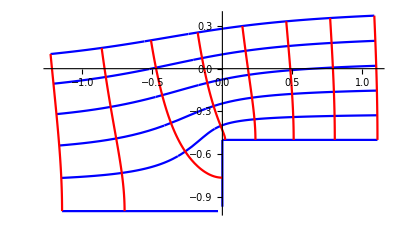

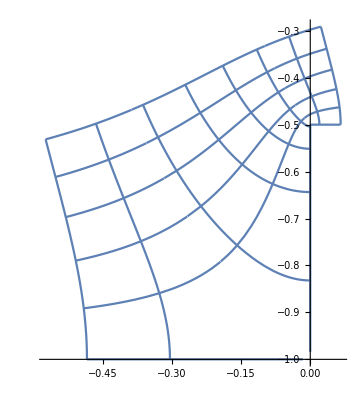

```mathematica
d=.5; h=1;
ff[ζ_]=f/.{KK->d/π,F-> -(h-d) ⅈ};
L=5;
Show[ParametricPlot[Array[ReIm@ff[ξ+ⅈ #]&,6,{-1,L}],{ξ,-L,2L},PlotStyle->{Blue},AspectRatio->Automatic],
 ParametricPlot[Array[ReIm@ff[#+ⅈ η]&,8,{-L,2L}],{η,-1,L},PlotStyle->{Red},AspectRatio->Automatic]]
```

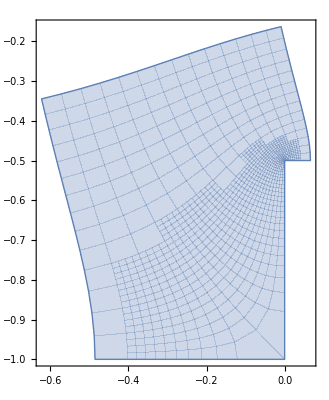

```mathematica
ParametricPlot[ReIm@ff[ξ+ⅈ η],{ξ,-2,2},{η,-1,2}]
```